```mathematica
agnr=ParallelTable[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/51AGNR/lead"<>ToString[x]<>".dat"]],{x,Range[0,3,0.01]}]
```

{{{0.+8.06296×10^-6 ⅈ,-1.06658+0. ⅈ,0.-0.000114721 ⅈ,0.0688734+0. ⅈ,0.+0.000121608 ⅈ,1.07877+0. ⅈ,91,-1.14764+0. ⅈ,0.+0.000215897 ⅈ,0.997706+0. ⅈ,0.-1.40502×10^-6 ⅈ,0.0665794+0. ⅈ},100,{1}},299,{1}}
 |  |  |  |

```mathematica
LEFTagnr[ω_,δ_,t_,ϵ_,m_]:= agnr[[Round[ω*100+1]]]
```

```mathematica
zgnr= ParallelTable[ToExpression[Import["/home/shardulmukim/PhD/fwi/zgnr/50zgnr/leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{1}
 |  |  |  |

```mathematica
LEFTzgnr[ω_,δ_,t_,ϵ_,m_]:= zgnr[[Round[ω*100+1]]]
```

```mathematica
βzgnr[ω_,δ_,t_,ϵ_,m_]:=βzgnr[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
Tzgnr[t_,m_]:=Tzgnr[t,m]=ReplacePart[0*IdentityMatrix[m],Join[Table[{x,x+1},{x,Range[1,m,4]}],Table[{x,x-1},{x,Range[4,m,4]}]]->t]
```

```mathematica
βagnr[ω_,δ_,t_,ϵ_,m_]:=
βagnr[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
Tagnr[t_,m_]:=Tagnr[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-LEFTzgnr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]].LEFTzgnr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]]].LEFTzgnr[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-LEFTzgnr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]].LEFTzgnr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]]].LEFTzgnr[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:=LEFTzgnr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].Tzgnr[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]]-Tzgnr[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris[ω_,δ_,t_,ϵ_,m_]:= If[tr1[ω,δ,t,ϵ,m]>25,25,tr1[ω,δ,t,ϵ,m]]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
unit[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Module[{b=βzgnr[ω,δ,t,ϵ,50]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{3,47}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
Clear[unit]
```

```mathematica
{Join[{unit[ω,0.0001,1,0,0,1]},RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,n1],10],Table[unit[ω,0.0001,1,0,ϵ1,n2],0] ,Table[unit[ω,0.0001,1,0,0,1],25-10]]],{unit[ω,0.0001,1,0,0,1]}]}
```

{{unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,ϵ1,n1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1],unit[ω,0.0001,1,0,0,1]}}

```mathematica
Dimensions[%28]
```

{1,27}

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,50](*,s[38,50,38,50]*)],concentration],RandomSample[Join[s[1,100,51,102](*,s[38,50,1,37]*)],total-concentration]],First],1000]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Inverse[Module[{J=βzgnr[ω,δ,t,ϵ,50],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
devicezgnr[ω_,δ_,t_,ϵ_,ϵ1_,m_,total_,concentration_,number_]:=Module[{list,b2},
sl1=Inverse[IdentityMatrix[m]-f[ω,δ,t,ϵ,ϵ1,1,total,concentration,number].Tzgnr[t,m].LEFTzgnr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]]].f[ω,δ,t,ϵ,ϵ1,1,total,concentration,number];sl2=Module[{J=sl1},Do[J=Inverse[IdentityMatrix[m]-f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number].Tzgnr[t,m].J.ConjugateTranspose[Tzgnr[t,m]]].f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number],{unitcell,2,50}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl2.ConjugateTranspose[Tzgnr[t,m]].LEFTzgnr[ω,0.0001,1,0,m].ConjugateTranspose[Tzgnr[t,m]]].sl2;
Ir1:=Inverse[IdentityMatrix[m]-LEFTzgnr[ω,0.0001,1,0,m].ConjugateTranspose[Tzgnr[t,m]].sl3.ConjugateTranspose[Tzgnr[t,m]]].LEFTzgnr[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= LEFTzgnr[ω,0.0001,1,0,m].ConjugateTranspose[Tzgnr[t,m]].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.Tzgnr[t,m].grr1.ConjugateTranspose[Tzgnr[t,m]]-Tzgnr[t,m].GNON1.ConjugateTranspose[Tzgnr[t,m]].GNON1]]]
```

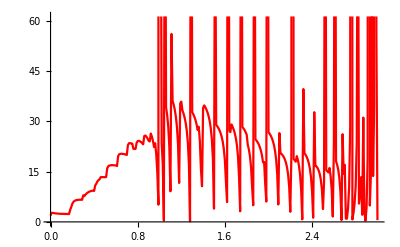

```mathematica
ListLinePlot[ParallelTable[{ω,devicezgnr[ω,0.0001,1,0,0,50,50,25,1]},{ω,Range[0,3,0.01]}],PlotStyle->Red]
```

```mathematica
ParallelTable[{ω,Print[ω];devicezgnr[ω,0.0001,1,0,0.5,50,50,25,1]},{ω,Range[0,3,0.01]}]
```

{{0.,0.0265897},{0.01,1.82163},{0.02,2.71269},{0.03,2.38437},{0.04,2.71431},{0.05,2.54595},{0.06,2.20762},{0.07,2.2807},{0.08,2.56524},{0.09,2.45435},{0.1,1.67127},{0.11,2.98999},{0.12,2.23469},{0.13,2.38387},{0.14,2.58562},{0.15,2.54714},{0.16,2.39018},{0.17,2.32779},{0.18,4.10291},{0.19,4.57572},{0.2,5.57723},{0.21,6.28156},{0.22,6.00187},{0.23,6.44228},{0.24,6.88893},{0.25,6.63606},{0.26,6.49185},{0.27,6.75818},{0.28,6.84188},{0.29,6.55326},{0.3,7.53014},{0.31,7.64254},{0.32,8.14808},{0.33,8.8487},{0.34,8.44018},{0.35,9.12027},{0.36,9.06113},{0.37,8.96698},{0.38,9.44136},{0.39,9.39475},{0.4,8.82488},{0.41,10.5669},{0.42,11.7674},{0.43,11.6846},{0.44,12.3226},{0.45,12.7333},{0.46,13.3291},{0.47,13.7169},{0.48,13.5783},{0.49,13.4727},{0.5,13.3664},{0.51,13.1307},{0.52,16.8634},{0.53,16.7765},{0.54,16.8718},{0.55,15.979},{0.56,16.6867},{0.57,17.384},{0.58,17.0877},{0.59,17.0636},{0.6,16.805},{0.61,16.8077},{0.62,17.6693},{0.63,18.2043},{0.64,18.7581},{0.65,19.8578},{0.66,19.9037},{0.67,19.5063},{0.68,20.0352},{0.69,20.0147},{0.7,19.4958},{0.71,22.339},{0.72,22.2084},{0.73,22.0146},{0.74,22.9672},{0.75,22.8814},{0.76,21.1801},{0.77,21.4779},{0.78,22.1284},{0.79,24.1627},{0.8,23.9421},{0.81,23.8715},{0.82,23.4841},{0.83,23.4228},{0.84,23.5505},{0.85,22.0627},{0.86,24.6814},{0.87,26.7192},{0.88,25.7219},{0.89,24.2095},{0.9,24.1402},{0.91,25.4528},{0.92,30.5505},{0.93,30.9921},{0.94,29.2129},{0.95,30.7429},{0.96,28.9653},{0.97,22.6748},{0.98,15.0473},{0.99,32.2969},{1.,71889.7},{1.01,326.686},{1.02,1.90566},{1.03,11.0548},{1.04,1.49947},{1.05,227.024},{1.06,31.4305},{1.07,21.9582},{1.08,20.2441},{1.09,16.5734},{1.1,11.8282},{1.11,58.9846},{1.12,33.2525},{1.13,32.4503},{1.14,32.6412},{1.15,27.1848},{1.16,23.5596},{1.17,17.6446},{1.18,22.0204},{1.19,59.6301},{1.2,34.5157},{1.21,30.2294},{1.22,30.539},{1.23,29.2961},{1.24,31.6384},{1.25,22.5837},{1.26,14.4547},{1.27,12.3302},{1.28,10.8783},{1.29,250.726},{1.3,30.2809},{1.31,29.9594},{1.32,28.4239},{1.33,28.0195},{1.34,29.0123},{1.35,26.5913},{1.36,22.8791},{1.37,11.6306},{1.38,1.83033},{1.39,49.0663},{1.4,71.4462},{1.41,31.0098},{1.42,29.7322},{1.43,29.0433},{1.44,28.1599},{1.45,26.3852},{1.46,28.3257},{1.47,22.3013},{1.48,18.1989},{1.49,15.9661},{1.5,21.2654},{1.51,141.825},{1.52,33.5808},{1.53,32.5445},{1.54,30.8483},{1.55,29.945},{1.56,31.4224},{1.57,29.8435},{1.58,30.1425},{1.59,19.6023},{1.6,14.2769},{1.61,19.0354},{1.62,13.8043},{1.63,261.108},{1.64,32.523},{1.65,31.4616},{1.66,28.7764},{1.67,28.1934},{1.68,28.263},{1.69,26.3377},{1.7,27.0823},{1.71,18.3491},{1.72,13.4059},{1.73,9.48692},{1.74,4.90624},{1.75,143.35},{1.76,28.1736},{1.77,27.0613},{1.78,26.5538},{1.79,25.7375},{1.8,26.1524},{1.81,22.161},{1.82,21.9437},{1.83,15.7521},{1.84,11.9455},{1.85,8.2256},{1.86,12.6633},{1.87,112.663},{1.88,23.2061},{1.89,22.3446},{1.9,23.3769},{1.91,21.403},{1.92,21.2653},{1.93,20.5119},{1.94,18.6915},{1.95,14.4274},{1.96,10.8774},{1.97,9.78009},{1.98,6.3463},{1.99,205.896},{2.,22.1277},{2.01,22.1928},{2.02,21.0632},{2.03,20.7021},{2.04,19.7554},{2.05,19.7763},{2.06,21.0137},{2.07,7.964},{2.08,0.892089},{2.09,1.823},{2.1,88.8193},{2.11,7.81086},{2.12,24.9331},{2.13,23.3433},{2.14,23.9529},{2.15,22.1232},{2.16,22.0055},{2.17,21.9855},{2.18,14.2325},{2.19,3.29268},{2.2,2.66496},{2.21,15.333},{2.22,482.638},{2.23,23.1285},{2.24,21.9141},{2.25,22.0732},{2.26,19.5067},{2.27,19.2058},{2.28,16.2679},{2.29,9.9539},{2.3,2.71038},{2.31,4.28333},{2.32,79.916},{2.33,14.4848},{2.34,18.8216},{2.35,18.5662},{2.36,17.8298},{2.37,18.7729},{2.38,16.3866},{2.39,11.3552},{2.4,4.68442},{2.41,8.41396},{2.42,23.5803},{2.43,59.9646},{2.44,15.874},{2.45,15.258},{2.46,15.3763},{2.47,15.6861},{2.48,9.89855},{2.49,3.44776},{2.5,1.72138},{2.51,1.16587},{2.52,77.7371},{2.53,14.2345},{2.54,14.4532},{2.55,13.7448},{2.56,14.3237},{2.57,12.1888},{2.58,2.60316},{2.59,5.4229},{2.6,32.8353},{2.61,264.367},{2.62,14.6398},{2.63,16.3451},{2.64,15.2456},{2.65,10.5966},{2.66,0.145231},{2.67,0.797786},{2.68,45.4404},{2.69,7.20293},{2.7,15.2571},{2.71,0.0465135},{2.72,2.30928},{2.73,13.487},{2.74,19.317},{2.75,56.0856},{2.76,124.091},{2.77,3.52304},{2.78,3.26116},{2.79,11.9956},{2.8,22.714},{2.81,32.776},{2.82,76.7192},{2.83,13.4742},{2.84,18.5354},{2.85,13.4478},{2.86,14.1235},{2.87,120.429},{2.88,3.3764},{2.89,1.31546},{2.9,0.809888},{2.91,12.9412},{2.92,130.183},{2.93,14.7355},{2.94,16.8858},{2.95,52.0999},{2.96,16.4143},{2.97,12.5639},{2.98,13.9817},{2.99,103.725},{3.,0.134609}}

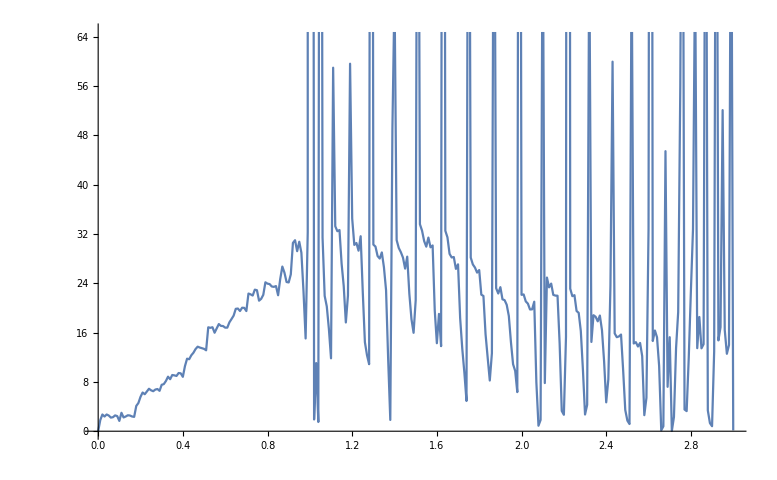

```mathematica
ListPlot[%43,Joined->True]
```

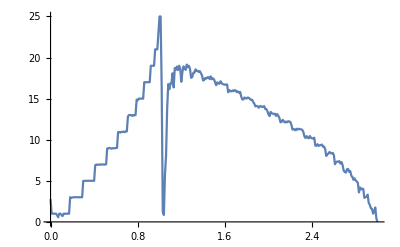

```mathematica
ListPlot[%20,Joined->True]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/zgnr/transmission_zgnr_imp_ca.dat",ca]
```

/home/shardulmukim/PhD/fwi/zgnr/transmission_zgnr_imp_ca.dat

```mathematica
transmission:=transmission=Import["/home/shardulmukim/PhD/fwi/zgnr/transmission_zgnr_imp.dat"]
```

```mathematica
ca:=Transpose[Join[{Range[0,2.96,0.01]},{MovingAverage[Transpose[transmission][[2]],5]}]]
```

```mathematica
Length[%33]
```

297

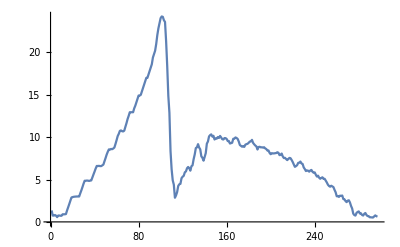

```mathematica
ListPlot[%33,Joined->True]
```

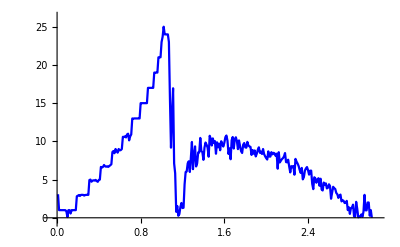

```mathematica
Show[%54,FrameLabel->{{HoldForm[Γ],None},{HoldForm[ω],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

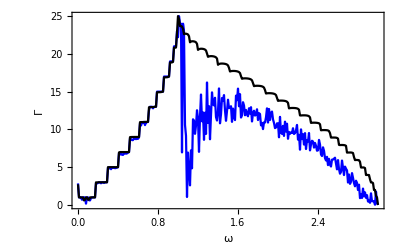

-Graphics-

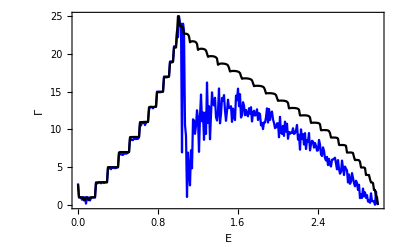

```mathematica
Show[%1,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

```mathematica
Table[Print["Working on === "<>ToString[5*num]<>"...."];Export["/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_"<>ToString[num]<>".DAT",Table[{ω,Mean[ParallelTable[devicezgnr[ω,0.0001,1,0,0.5,50,num,0,5,0],2000]]},{ω,Range[0.01,3,0.01]}]],{num,Range[2,25,2]}]
```

Working on === 10....

Working on === 20....

Working on === 30....

Working on === 40....

Working on === 50....

Working on === 60....

Working on === 70....

Working on === 80....

Working on === 90....

Working on === 100....

Working on === 110....

Working on === 120....

{/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_2.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_4.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_6.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_8.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_10.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_12.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_14.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_16.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_18.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_20.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_22.DAT,/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_24.DAT}

```mathematica
27*50
```

1350

```mathematica
LEFTagnrlead[ω_,δ_,t_,ϵ_,m_]:=LEFTagnrlead[ω,δ,t,ϵ,m]=Module[{J=Inverse[βagnr[ω,δ,t,ϵ,m]],B:=Inverse[βagnr[ω,δ,t,ϵ,m]],T1:=Tagnr[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,117366]; J=J]
```

```mathematica
devicezgnrsmall[ω_,δ_,t_,ϵ_,ϵ1_,m_,num1_,num2_,n1_,n2_]:=Module[{list,b2},
list={Join[{unit[ω,0.0001,1,0,0,1]},RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,n1],num1],Table[unit[ω,0.0001,1,0,ϵ1,n2],num2] ,Table[unit[ω,0.0001,1,0,0,1],5-num2-num1]]],{unit[ω,0.0001,1,0,0,1]}]};
sl1=Inverse[IdentityMatrix[m]-Inverse[list[[1,1]]].Tzgnr[t,m].LEFTzgnr[ω,δ,t,ϵ,m].ConjugateTranspose[Tzgnr[t,m]]].Inverse[list[[1,1]]];sl2=Module[{J=sl1},Do[J=Inverse[IdentityMatrix[m]-Inverse[list[[1,ζ]]].Tzgnr[t,m].J.ConjugateTranspose[Tzgnr[t,m]]].Inverse[list[[1,ζ]]],{ζ,2,6}];
 J=J];
sl3=Inverse[IdentityMatrix[m]-Inverse[list[[1,7]]].Tzgnr[t,m].sl2.ConjugateTranspose[Tzgnr[t,m]]].Inverse[list[[1,7]]];
Il1:=Inverse[IdentityMatrix[m]-sl3.ConjugateTranspose[Tzgnr[t,m]].LEFTzgnr[ω,0.0001,1,0,m].ConjugateTranspose[Tzgnr[t,m]]].sl3;
Ir1:=Inverse[IdentityMatrix[m]-LEFTzgnr[ω,0.0001,1,0,m].ConjugateTranspose[Tzgnr[t,m]].sl3.ConjugateTranspose[Tzgnr[t,m]]].LEFTzgnr[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= LEFTzgnr[ω,0.0001,1,0,m].ConjugateTranspose[Tzgnr[t,m]].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tzgnr[t,m].grr1.ConjugateTranspose[Tzgnr[t,m]]-Tzgnr[t,m].GNON1.ConjugateTranspose[Tzgnr[t,m]].GNON1]]>pris[ω,0.0001,1,0,m],pris[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tzgnr[t,m].grr1.ConjugateTranspose[Tzgnr[t,m]]-Tzgnr[t,m].GNON1.ConjugateTranspose[Tzgnr[t,m]].GNON1]]]]
```

```mathematica
h[num1_,num2_,n1_,n2_]:=Export["/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_"<>ToString[n1*num1+num2*n2]<>".DAT",Table[{ω,Mean[ParallelTable[devicezgnrsmall[ω,0.0001,1,0,0.5,50,num1,num2,n1,n2],2000]]},{ω,Range[0.01,3,0.01]}]]
```

```mathematica
h[5,0,2,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_10.DAT

```mathematica
h[5,0,3,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_15.DAT

```mathematica
h[5,0,4,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_20.DAT

```mathematica
h[5,0,5,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_25.DAT

```mathematica
h[5,0,6,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_30.DAT

```mathematica
h[3,2,9,4]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_35.DAT

```mathematica
h[5,0,8,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_40.DAT

```mathematica
h[5,0,9,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_45.DAT

```mathematica
h[5,0,10,0]
```

/home/shardulmukim/PhD/fwi/zgnr/50zgnr/CA_device_5agnr_50.DAT